```mathematica
c1=Lighter[Red,.6];c2=Lighter[Red,.4];c3=Lighter[Blue,.4];
ticks={{{{1,"MC"},{2,"BCL"},{3,"NC"}},None},{{{1,"CAM"},{2,"SIL"},{3,"ORS"},{4,"ML"},{5,"CM"}},None}};
```

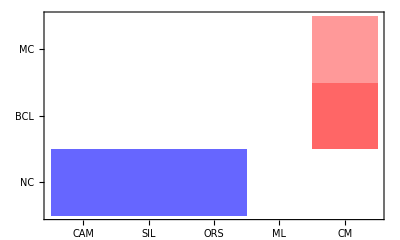

```mathematica
GRE1=ArrayPlot[{{c1,0,0,0,0},{c2,0,0,0,0},{c3,0,0,0,0}},Frame->True,FrameTicks->ticks];
COA1=ArrayPlot[{{0,0,0,0,c1},{0,0,0,0,c2},{c3,0,0,0,0}},Frame->True,FrameTicks->ticks];
COA2a=ArrayPlot[{{0,0,0,0,c1},{0,0,0,0,c2},{c3,c3,0,0,0}},Frame->True,FrameTicks->ticks];
COA2b=ArrayPlot[{{0,0,0,0,c1},{0,0,0,c2,0},{c3,c3,0,0,0}},Frame->True,FrameTicks->ticks];
COA4=ArrayPlot[{{0,0,0,0,c1},{0,0,0,0,c2},{c3,c3,c3,0,0}},Frame->True,FrameTicks->ticks]
GRE1=ArrayPlot[{{c1,0,0,0,0},{c2,0,0,0,0},{c3,0,0,0,0}},Frame->True,FrameTicks->ticks];
GRE2=ArrayPlot[{{0,c1,0,0,0},{0,c2,0,0,0},{c3,c3,0,0,0}},Frame->True,FrameTicks->ticks];
GRE3a=ArrayPlot[{{0,c1,0,0,0},{0,c2,0,0,0},{c3,c3,c3,0,0}},Frame->True,FrameTicks->ticks];
DEV2a=ArrayPlot[{{0,0,0,0,c1},{0,0,0,c2,0},{c3,c3,c3,0,0}},Frame->True,FrameTicks->ticks];
DEV2b=ArrayPlot[{{0,0,0,0,c1},{0,c2,c2,c2,0},{c3,c3,0,0,0}},Frame->True,FrameTicks->ticks];
DEV3=ArrayPlot[{{0,0,0,0,c1},{0,0,0,c2,0},{0,0,c3,0,0}},Frame->True,FrameTicks->ticks];
```

```mathematica
data={{"S0",GRE1,"","","","",""},{"S2",GRE1,COA1,COA1,"","",""},{"S2",GRE1,COA1,COA1,GRE1,"",""},{"S3",GRE1,COA2a,COA2a,GRE1,COA2a,""},
{"S4",GRE2,COA2a,COA2a,COA2b,COA2b,""},
{"S5",GRE2,COA4,COA2a,COA2b,COA2b,""},
{"S6",GRE3a,COA2b,COA2b,COA2b,DEV2b,DEV2a},
{"S7",GRE3a,DEV3,DEV3,COA2b,DEV2b,DEV2a},
{"S8",DEV3,DEV3,DEV3,DEV3,DEV3,DEV3}
};
itS1={{3,13,13,13,13,13,13}};
data2={{"S0","GRE.1a","","","","",""},
{"S1","GRE.1a","COA.1","COA.1","","",""},
{"S2","GRE.1a","COA.1","COA.1","GRE.1a","",""},
{"S3","GRE.1b","COA.3, COA.2a","COA.2a","GRE.1b","COA.2a",""},
{"S4","GRE.2","COA.2a","COA.2a","COA.2b","COA.2b",""},
{"S5","GRE.2","COA.4","COA.2a","COA.2b","COA.2b",""},
{"S6","GRE.3a","COA.2b","COA.2b","COA.2b","DEV.2b","DEV.2a"},
{"S7","GRE.3a","DEV.3","DEV.3","COA.2b","DEV.2b","DEV.2a"},
{"S8","DEV.3","DEV.3","DEV.3","DEV.3","DEV.3","DEV.3"}
};
itS2={{3,7,7,7,7,7,7}};
plot=Text@Grid[Prepend[data2,{"Time","DLB","MUR","LYE","PHI","SED","AUS"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Center,ItemSize->itS2,Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Time | DLB | MUR | LYE | PHI | SED | AUS
S0 | GRE.1a |  |  |  |  | 
S1 | GRE.1a | COA.1 | COA.1 |  |  | 
S2 | GRE.1a | COA.1 | COA.1 | GRE.1a |  | 
S3 | GRE.1b | COA.3, COA.2a | COA.2a | GRE.1b | COA.2a | 
S4 | GRE.2 | COA.2a | COA.2a | COA.2b | COA.2b | 
S5 | GRE.2 | COA.4 | COA.2a | COA.2b | COA.2b | 
S6 | GRE.3a | COA.2b | COA.2b | COA.2b | DEV.2b | DEV.2a
S7 | GRE.3a | DEV.3 | DEV.3 | COA.2b | DEV.2b | DEV.2a
S8 | DEV.3 | DEV.3 | DEV.3 | DEV.3 | DEV.3 | DEV.3

```mathematica
SetDirectory["/home/carla/GDC/RUD_Pictures/"];
Export["GDC_RUD_InterpSch.jpeg",plot]
```

GDC_RUD_InterpSch.jpeg